## Define function pieces

#### Temperature/therm velocity stuff

```mathematica
T=75;(*in eV*)
c=3*^8;
m=511000/c^2;(*eV/c^2 *)
vth[T_]:=√(2T /m) 
vthSq[T_]:=2T /m
```

```mathematica
w[T_,κ_]:=vth[T] √(1 - 3/(2κ))
```

```mathematica
wSq[T_,κ_]:=vthSq[T] (1 - 3/(2κ))
```

```mathematica
w[T,1.6]
```

1.28498×10^6

#### Bulk velocity stuff

```mathematica
pot=1000;(*in eV*)
vb =  √(2 pot / m)
```

300000000 √(2/511)

```mathematica
vbSq=2pot/m;
```

```mathematica
(*vbprime[vb_,T_,κ_]:=vb/(√κ w[T,κ])
vbprimeSq[vb_,T_,κ_]:=vb^2/(κ wSq[T,κ])*)
```

#### Kappa and α stuff

```mathematica
κ=3;
kappaListSmall={1.6,1.9,2.5,4.0,8.0};
kappaList=Range[2.0,20,0.1];
```

```mathematica
α = 1/30;
alphaList=PowerRange[0.0005,0.999,1.05];
```

## a Functions

```mathematica
a[x_,κ_,b_,vb_,T_]:=1+1/κ(b^2 vb^2/wSq[T,κ]+b (b-1) x^2+2 b (b-1)vb/w[T,κ] x)
aNegkappaPlusOneHalf[x_,κ_,b_,vb_,T_] := (a[x,κ,b,vb,T])^(-κ+1/2)
```

## Eta Functions

```mathematica
etaCoeff[κ_,b_,vb_,T_] :=(2 vb)/w[T,κ] (1-b) (1/2(κ^(3/2)Gamma[κ-1/2])/Gamma[κ+1]+(vb/w[T,κ])/(√Pi) Hypergeometric2F1[1/2,κ,3/2,(-(vb/w[T,κ])^2)/κ])^-1
etaintegrand1[x_,κ_,b_,vb_,T_] := 1/(2 √(1-b)) (κ^(3/2)Gamma[κ-1/2])/Gamma[κ+1] aNegkappaPlusOneHalf[x,κ,b,vb,T]
etaintegrand2[x_,κ_,b_,vb_,T_] := x/(√π) ((a[x,κ,b,vb,T])^-κ) Hypergeometric2F1[1/2,κ,3/2,-((1-b) x^2)/a[x,κ,b,vb,T]]
etaintegrand[x_,κ_,b_,vb_,T_] := etaintegrand1[x,κ,b,vb,T]-etaintegrand2[x,κ,b,vb,T]
```

### Now Plots

#### Try the whole thing

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {23.5397}. NIntegrate obtained 1.42429×10^9+3.51313×10^8 ⅈ and 1.56048×10^9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {15.829}. NIntegrate obtained 1.87832×10^10+1.32045×10^7 ⅈ and 1.8779×10^10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {12.4733}. NIntegrate obtained 1.25335×10^13+7.6789×10^7 ⅈ and 1.3236×10^13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

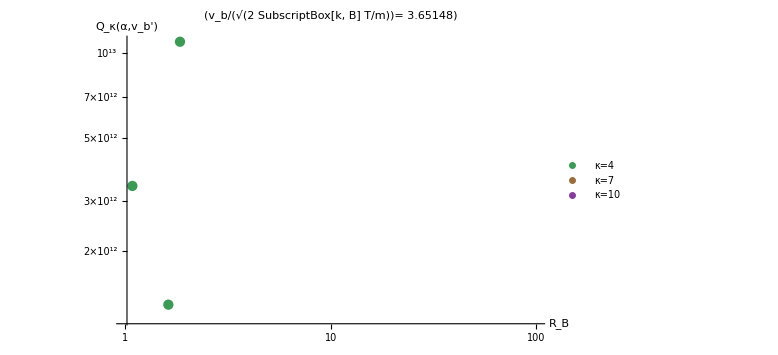

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vb/w[T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{{1,100},Automatic},PlotLegends->LineLegend[Automatic],ImageSize->Large, PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10}}]]
```

#### Doesn’t work, so try first term

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {23.5397}. NIntegrate obtained 2.84858×10^9+2.34208×10^8 ⅈ and 3.02224×10^9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {15.829}. NIntegrate obtained 3.75663×10^10+8.80298×10^6 ⅈ and 3.7558×10^10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {12.4733}. NIntegrate obtained 2.50669×10^13+5.11927×10^7 ⅈ and 2.6472×10^13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

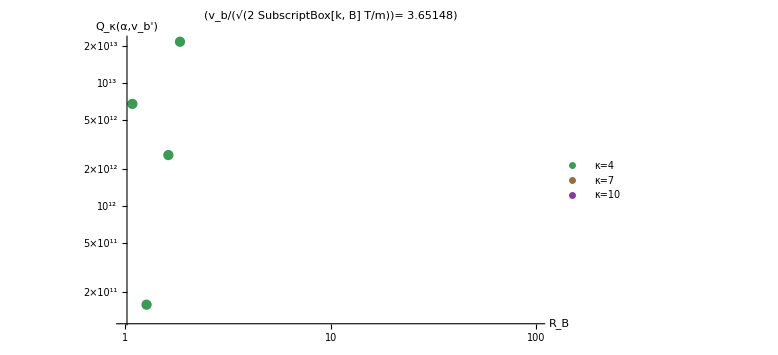

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand1[x,k,alpha,vb,T],{x,-vb/w[T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{{1,100},Automatic},PlotLegends->LineLegend[Automatic],ImageSize->Large, PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10}}]]
```

#### Nope! Try second term

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {23.5397}. NIntegrate obtained 1.42429×10^9-1.17104×10^8 ⅈ and 1.51112×10^9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {15.829}. NIntegrate obtained 1.87832×10^10-4.40149×10^6 ⅈ and 1.8779×10^10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {12.4733}. NIntegrate obtained 1.25335×10^13-2.55963×10^7 ⅈ and 1.3236×10^13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

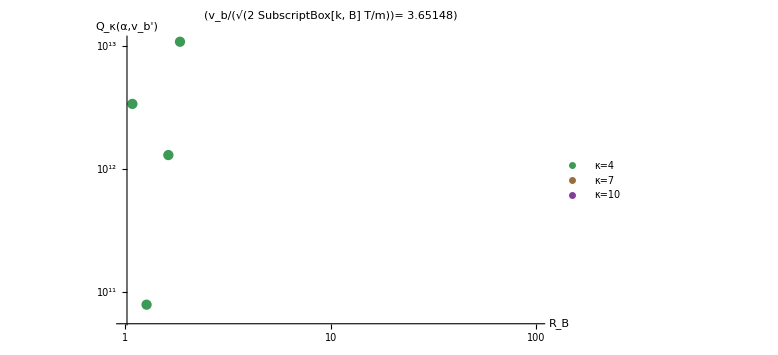

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand2[x,k,alpha,vb,T],{x,-vb/w[T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{{1,100},Automatic},PlotLegends->LineLegend[Automatic],ImageSize->Large, PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10}}]]
```

#### NOPE! OK … just the coefficient

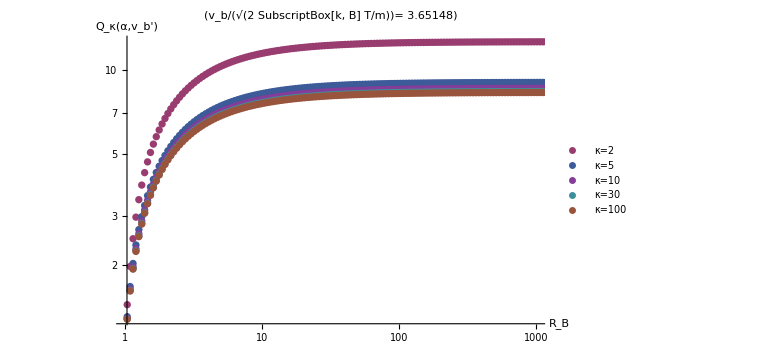

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{{1,1000},Automatic},PlotLegends->LineLegend[Automatic],ImageSize->Large, PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{2,5,10,30,100}}]]
```

#### Just the Γ part of term 1

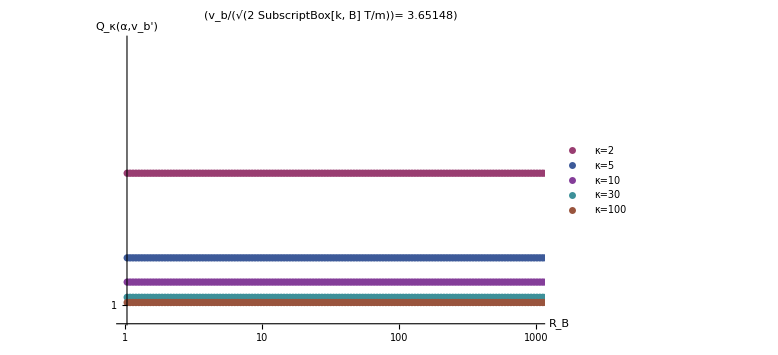

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,(k^(3/2)Gamma[k-1/2])/Gamma[k+1]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{{1,1000},Automatic},PlotLegends->LineLegend[Automatic],ImageSize->Large, PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{2,5,10,30,100}}]]
```

#### Looks nice, so how about a?

```mathematica
alpha=0.5;
```

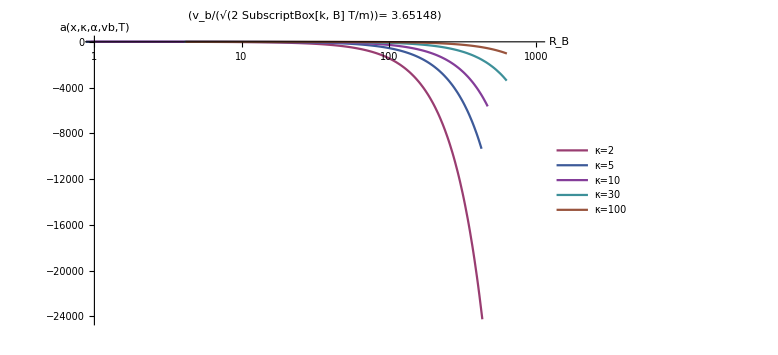

```mathematica
Show[Table[LogLinearPlot[Legended[a[x,k,alpha,vb,T],StringForm["κ=`1`",NumberForm[k,2]]],{x,-vb/w[T,k],1000},PlotStyle->ColorData[1][k],PlotRange->{{1,1000},Automatic},PlotLegends->LineLegend[Automatic],ImageSize->Large, PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["a(x,κ,α,vb,T)"]}],{k,{2,5,10,30,100}}]]
```

```mathematica
k=2.0;
```

```mathematica
data=N[Table[{x,a[x,k,alpha,vb,T]},{x,-vb/w[T,k],100}]]
```

{{-7.30297,14.3333},{-6.30297,14.2083},{-5.30297,13.8333},{-4.30297,13.2083},{-3.30297,12.3333},{-2.30297,11.2083},{-1.30297,9.83333},{-0.302967,8.20833},{0.697033,6.33333},{1.69703,4.20833},{2.69703,1.83333},{3.69703,-0.791667},{4.69703,-3.66667},{5.69703,-6.79167},{6.69703,-10.1667},{7.69703,-13.7917},{8.69703,-17.6667},{9.69703,-21.7917},{10.697,-26.1667},{11.697,-30.7917},{12.697,-35.6667},{13.697,-40.7917},{14.697,-46.1667},{15.697,-51.7917},{16.697,-57.6667},{17.697,-63.7917},{18.697,-70.1667},{19.697,-76.7917},{20.697,-83.6667},{21.697,-90.7917},{22.697,-98.1667},{23.697,-105.792},{24.697,-113.667},{25.697,-121.792},{26.697,-130.167},{27.697,-138.792},{28.697,-147.667},{29.697,-156.792},{30.697,-166.167},{31.697,-175.792},{32.697,-185.667},{33.697,-195.792},{34.697,-206.167},{35.697,-216.792},{36.697,-227.667},{37.697,-238.792},{38.697,-250.167},{39.697,-261.792},{40.697,-273.667},{41.697,-285.792},{42.697,-298.167},{43.697,-310.792},{44.697,-323.667},{45.697,-336.792},{46.697,-350.167},{47.697,-363.792},{48.697,-377.667},{49.697,-391.792},{50.697,-406.167},{51.697,-420.792},{52.697,-435.667},{53.697,-450.792},{54.697,-466.167},{55.697,-481.792},{56.697,-497.667},{57.697,-513.792},{58.697,-530.167},{59.697,-546.792},{60.697,-563.667},{61.697,-580.792},{62.697,-598.167},{63.697,-615.792},{64.697,-633.667},{65.697,-651.792},{66.697,-670.167},{67.697,-688.792},{68.697,-707.667},{69.697,-726.792},{70.697,-746.167},{71.697,-765.792},{72.697,-785.667},{73.697,-805.792},{74.697,-826.167},{75.697,-846.792},{76.697,-867.667},{77.697,-888.792},{78.697,-910.167},{79.697,-931.792},{80.697,-953.667},{81.697,-975.792},{82.697,-998.167},{83.697,-1020.79},{84.697,-1043.67},{85.697,-1066.79},{86.697,-1090.17},{87.697,-1113.79},{88.697,-1137.67},{89.697,-1161.79},{90.697,-1186.17},{91.697,-1210.79},{92.697,-1235.67},{93.697,-1260.79},{94.697,-1286.17},{95.697,-1311.79},{96.697,-1337.67},{97.697,-1363.79},{98.697,-1390.17},{99.697,-1416.79}}

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,a[x_,k,alpha,vb,T]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{{1,1000},Automatic},PlotLegends->LineLegend[Automatic],ImageSize->Large, PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{2,5,10,30,100}}]]
```

```mathematica
alpha=0.5;
```

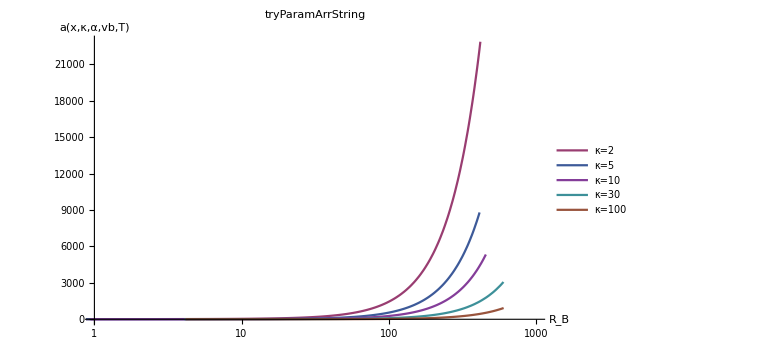

```mathematica
Show[Table[LogLinearPlot[Legended[a[x,k,alpha,vb,T],StringForm["κ=`1`",NumberForm[k,2]]],{x,-vb/w[T,k],1000},PlotStyle->ColorData[1][k],PlotRange->{{1,1000},Automatic},PlotLegends->LineLegend[Automatic],ImageSize->Large, PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["a(x,κ,α,vb,T)"]}],{k,{2,5,10,30,100}}]]
```

```mathematica
alpha=0.5;
```

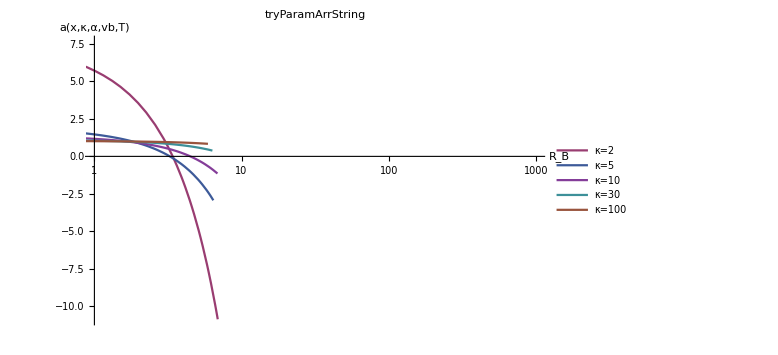

```mathematica
Show[Table[LogLinearPlot[Legended[a[x,k,alpha,vb,T],StringForm["κ=`1`",NumberForm[k,2]]],{x,-vb/w[T,k],10},PlotStyle->ColorData[1][k],PlotRange->{{1,1000},Automatic},PlotLegends->LineLegend[Automatic],ImageSize->Large, PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["a(x,κ,α,vb,T)"]}],{k,{2,5,10,30,100}}]]
```

```mathematica
ZprimeUp=
```